```mathematica
(*Approximation de la probabilité de ruine ultime*)
(*Developpement de densité de probabilité bivariée*)
(*La mesure de référence choisi est la loi Gamma de paramètre ξ et ν*)
muGamma=Function[{x,m,r},(1/m)^(r)*Exp[-x/m]*x^(r-1)/Gamma[r]];
(*Polynôme mu orthogonaux associé*)
QnGamma=Function[{n,x,m,r},(-1)^n*LaguerreL[n,r-1,x/m]/Sqrt[Binomial[n+r-1,n]]];
(*Loi Poisson de paramètre λ*)
FoncGenPoisson=Function[{s,λ},Exp[λ(s-1)]-Exp[-λ]];
(*Distribution Gamma*)
LaplaceGamma=Function[{s,α,β},(1/(1-s*β))^(α)];
LaplaceCompoundPoissonGamma=Function[{s,λ,α,β},FoncGenPoisson[LaplaceGamma[s,α,β],λ]];
CoefGenFunctionCompoundPoissonGamma=Function[{λ,α,β,z,m,r},FullSimplify[(1+z)^(-r)*LaplaceCompoundPoissonGamma[z/m/(1+z),λ,α,β]]];
ExpansionCoefficientCompoundPoissonGamma=Function[{λ,α,β,z,m,r,K},Expansion=Normal[Series[CoefGenFunctionCompoundPoissonGamma[λ,α,β,z,m,r],{z,0,K}]];Table[1/Sqrt[Binomial[i+r-1,i]]/(i!)*(D[Expansion,{z,i}]/.z->0),{i,0,K}]];
(*Poisson coposée avec des sinistres de loi exponentielles*)
DensityCompoundPoissonExponential=Function[{x,λ,β},Exp[-(λ+x/β)]*Sqrt[λ/β/x]*BesselI[1,2Sqrt[λ*x/β]]];
NaiveDensityCompoundPoissonGamma=Function[{x,λ,α,β,KNaive},
Sum[Exp[-λ]*λ^(k)/k!*PDF[GammaDistribution[k*α,β],x],{k,1,KNaive}
]
];
NaiveSurvivalCompoundPoissonGamma=Function[{u,λ,α,β,KNaive},
Sum[Exp[-λ]*λ^(k)/k!*SurvivalFunction[GammaDistribution[k*α,β],u],{k,1,KNaive}]
];
(*Système de polynômes orthogonaux*)
Qnm=Function[{x,m,r,K},Table[QnGamma[i,x,m,r]muGamma[x,m,r],{i,0,K}]];
DensityExpansion=Function[{VectorCoef,x,m,r,K},Total[VectorCoef[[1;;K+1]]*Qnm[x,m,r,K]]];
SurvivalExpansion=Function[{VectorCoef,u,m,r,K},Integrate[DensityExpansion[VectorCoef,x,m,r,K],{x,u,+∞},Assumptions->Im[u]≠0||Re[u]>0]];
UsualStopLossPremiumExpansion=Function[{VectorCoef,c,m,r,K},
Integrate[SurvivalExpansion[VectorCoef,u+c,m,r,K]
,{u,0,+∞}]];
(*Evaluation de la probabilité de ruine via ls FFT*)
(*Fonction de sur£vie via les FFT*)
(*Calcul des Sn*)
FoncGenPoissonFFT=Function[{s,λ},Exp[λ(s-1)]];
LaplaceCompoundPoissonGammaSurvival=Function[{s,λ,α,β},(1-FoncGenPoissonFFT[LaplaceGamma[-s,α,β],λ])/s];
SnCompoundPoissonGammaSurvival=Function[{b,u,n,λ,α,β},Exp[b/2]/2/u*Re[LaplaceCompoundPoissonGammaSurvival[b/2/u,λ,α,β]]+Exp[b/2]/u*Sum[(-1)^(i)*Re[LaplaceCompoundPoissonGammaSurvival[(b+I*i*2π)/2/u,λ,α,β]],{i,1,n,1}]];
SurvivalCompoundPoissonGammaFFT=Function[{m,b,u,n,λ,α,β},Sum[Binomial[m,i]*2^(-m)SnCompoundPoissonGammaSurvival[b,u,n+i,λ,α,β],{i,0,m,1}]];
(*Evaluation de la probabilité de ruine via la scaled laplace Transform*)
LaplaceCompoundPoissonGammaMnats=Function[{s,λ,α,β},FoncGenPoissonFFT[LaplaceGamma[-s,α,β],λ]];
(*Formule de la densité et transformée de Laplace de la probabilité de ruine*)
SurvivalCompoundPoissonGammaMnats=Function[{λ,α,β,αMnats,bMnats,u},
Sum[
Sum[
Binomial[αMnats,j]*Binomial[j,k](-1)^(j-k)LaplaceCompoundPoissonGammaMnats[Log[bMnats]*j,λ,α,β]
,{j,k,αMnats}]
,{k,0,Floor[αMnats*Exp[-u*Log[bMnats]]]}
]];
DensityCompoundPoissonGammaMnats=Function[{λ,α,β,αMnats,bMnats,x},
Floor[αMnats*Exp[-Log[bMnats]*x]]Log[bMnats]Gamma[αMnats+2]/(αMnats*Gamma[Floor[αMnats*Exp[-Log[bMnats]*x]]+1])*
Sum[
(-1)^(j)*LaplaceCompoundPoissonGammaMnats[j+Floor[αMnats*Exp[-Log[bMnats]*x]],λ,α,β]/j!/(αMnats-Floor[αMnats*Exp[-Log[bMnats]*x]]-j)!
,{j,0,αMnats-Floor[αMnats*Exp[-Log[bMnats]*x]]}]
];
SurvivalCompoundPoissonGammaMnatsBis=Function[{λ,α,β,αMnats,bMnats,x},
Floor[αMnats*Exp[-Log[bMnats]*x]]Log[bMnats]Gamma[αMnats+2]/(αMnats*Gamma[Floor[αMnats*Exp[-Log[bMnats]*x]]+1])*
Sum[
(-1)^(j)*LaplaceCompoundPoissonGammaSurvival[j+Floor[αMnats*Exp[-Log[bMnats]*x]],λ,α,β]/j!/(αMnats-Floor[αMnats*Exp[-Log[bMnats]*x]]-j)!
,{j,0,αMnats-Floor[αMnats*Exp[-Log[bMnats]*x]]}]
];
(*Algorithme de Panjer*)
(*Discrétisation, h représente le pas de discrétisation, u est la limite, on créer un vecteur de taille u/h*)
DiscretizeGamma=Function[{α,β,umax,h},PartitionGrid=Table[k*h,{k,0,umax/h,1}];ProbaU=Table[N[CDF[GammaDistribution[α,β],Max[PartitionGrid[[i]]+h/2,0]]-CDF[GammaDistribution[α,β],Max[PartitionGrid[[i]]-h/2,0]]],{i,1,Length[PartitionGrid](*-1*),1}]];
ProbaDiscretePoissonCompoundGamma=Function[{λ,h,VectProbaU,umax},ProbaCompoundPoisson={};AppendTo[ProbaCompoundPoisson,Exp[-λ]];
For[j=1,j<umax/h+1,j++,AppendTo[ProbaCompoundPoisson,Sum[λ*k/j*VectProbaU[[k]]*ProbaCompoundPoisson[[(j-k)+1]],{k,1,j,1}]]];ProbaCompoundPoisson];
SurvivalPoissonCompoundGammaPanger=Function[{VectProbaCompoundPoisson,h,u},1-Sum[VectProbaCompoundPoisson[[k]],{k,1,u/h}]];
```

```mathematica
(*Sinistres de loi gamma*)
α=1;
β=2;
(*Fréquence des sinistres de loi de Poisson*)
λ=4;
(*Moment d'ordre 1 et 2 de la distribution composée*)
μX=λ*Mean[GammaDistribution[α,β]];
VarX=λ*Mean[GammaDistribution[α,β]]+Moment[GammaDistribution[α,β],2]*λ;
(*Coefficient de la représentation polynomiale*)
NbParametrization=3;
m={β,N[μX],VarX/μX}
r={α,1,μX^(2)/VarX}
(*Fonction génératrice des coefficients*)(*Table[CoefGenFunctionCompoundPoissonGamma[λ,α,β,z,m[[i]],r[[i]]],{i,1,NbParametrization}]*)
```

{2,8.,5}

{1,1,8/5}

```mathematica
(*Coefficients et polynômes orthogonaux*)
KPoly=30;
MatrixForm[N[VectorCoef=Table[ExpansionCoefficientCompoundPoissonGamma[λ,α,β,z,m[[i]],r[[i]],KPoly],{i,1,NbParametrization}]]]
(*Approximation de la densité*)
MatrixForm[DensityCompoundPoissonGammaPolynomial=Table[DensityExpansion[VectorCoef[[i]],x,m[[i]],r[[i]],KPoly],{i,1,NbParametrization}]];
MatrixForm[SurvivalCompoundPoissonGammaPolynomial=Table[SurvivalExpansion[VectorCoef[[i]],u,m[[i]],r[[i]],KPoly],{i,1,NbParametrization}]];
UsualStopLossCompoundPoissonGammaPolynomial=UsualStopLossPremiumExpansion[VectorCoef[[1]],c,m[[1]],r[[1]],KPoly];
```

(0.981684 | 3.01832 | 4.98168 | 5.68498 | 4.98168 | 3.55165 | 2.13724 | 1.11355 | 0.511843 | 0.210555 | 0.0784039 | 0.0266722 | 0.00835317 | 0.00242388 | 0.000655278 | 0.000165829 | 0.0000394475 | 8.85294×10^-6 | 1.8805×10^-6 | 3.79172×10^-7 | 7.27625×10^-8 | 1.33202×10^-8 | 2.33118×10^-9 | 3.90798×10^-10 | 6.28659×10^-11 | 9.72032×10^-12 | 1.4468×10^-12 | 2.07594×10^-13 | 2.87488×10^-14 | 3.84931×10^-15 | 4.9616×10^-16
0.981684 | 0.0183156 | -0.268316 | 0.247482 | -0.158941 | 0.0774302 | -0.0223304 | -0.00789111 | 0.0205339 | -0.0227643 | 0.0198631 | -0.0151441 | 0.0104087 | -0.00646225 | 0.00353051 | -0.0015454 | 0.000320864 | 0.0003506 | -0.000652268 | 0.000727138 | -0.000677364 | 0.000570525 | -0.00044786 | 0.000332067 | -0.000233688 | 0.00015588 | -0.0000977319 | 0.0000564182 | -0.0000285084 | 0.0000106861 | -9.04958×10^-8
0.981684 | 0.0231677 | -0.137355 | 0.0559428 | 0.00863332 | -0.0337896 | 0.0366942 | -0.032004 | 0.0266321 | -0.0226516 | 0.0201176 | -0.0185575 | 0.0175342 | -0.0167712 | 0.0161269 | -0.0155405 | 0.0149914 | -0.0144749 | 0.0139907 | -0.0135387 | 0.0131179 | -0.0127264 | 0.0123616 | -0.0120213 | 0.0117029 | -0.0114044 | 0.0111237 | -0.0108594 | 0.0106098 | -0.0103737 | 0.01015)

{0.0732626,0.146525,0.195367,0.195367,0.156293,0.104196,0.0595404,0.0297702,0.0132312,0.00529248,0.00192454,0.000641512,0.000197388,0.0000563967,0.0000150391,3.75978×10^-6,8.84654×10^-7,1.9659×10^-7,4.13873×10^-8,8.27746×10^-9,1.57666×10^-9,2.86665×10^-10,4.98549×10^-11,8.30914×10^-12,1.32946×10^-12,2.04533×10^-13,3.03011×10^-14,4.32874×10^-15,5.97067×10^-16,7.96089×10^-17}

```mathematica
(*Application de l'algoo de Panjer*)
h=1/100;
umax=30;
VectProbaU=DiscretizeGamma[α,β,umax,h];
VectProbaCompoundPoisson=ProbaDiscretePoissonCompoundGamma[λ,h,VectProbaU,umax];
```

```mathematica
(*Survival Function Via Inversion of Fourier*)
bFFT=18.5;
mFFT=11;
nFFT=15;
uFFT=10;
(*Paramétrisation Mnatskanov*)
αMnats=32;
bMnats=1.115;
(*Comparaison des valeurs*)
(*N[SurvivalCompoundPoissonGammaMnats[λ,α,β,αMnats,bMnats,uFFT]]
SurvivalCompoundPoissonGammaFFT[mFFT,bFFT,uFFT,nFFT,λ,α,β]
N[SurvivalCompoundPoissonGammaPolynomial[[1]]/.u->uFFT]
SurvivalPoissonCompoundGammaPanger[VectProbaCompoundPoisson,h,uFFT]*)
```

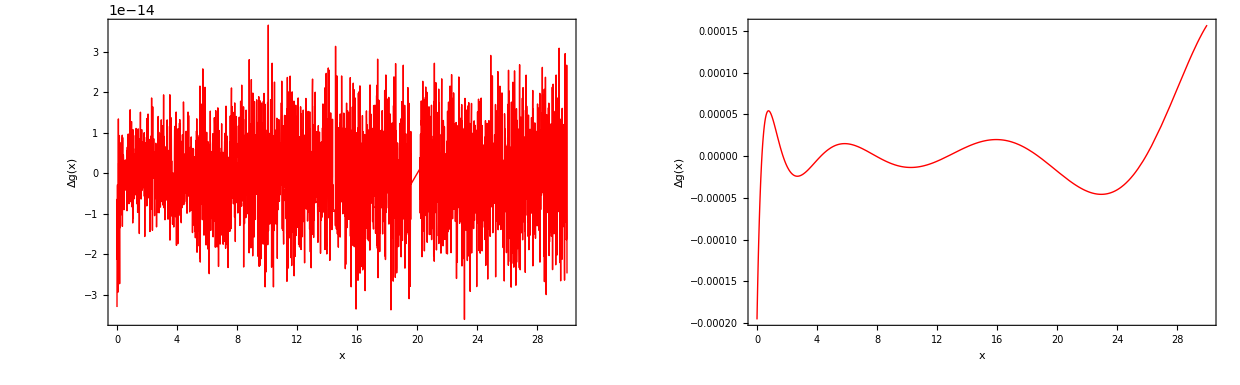

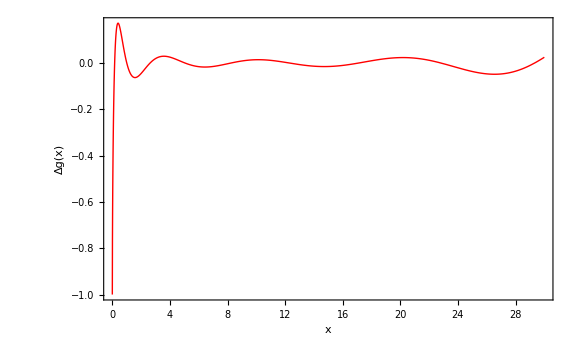

```mathematica
(*Graph D'erreur relative Pour différentes paramétrisations*)
(*Densité de probabilité*)
GraphicsGrid[{{Plot[(DensityCompoundPoissonGammaPolynomial[[1]]-DensityCompoundPoissonExponential[x,λ,β])/DensityCompoundPoissonExponential[x,λ,β],{x,0,umax},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,FrameLabel->{{Style["Δg(x)",24],None},{Style["x",24],Style["Parametrization 1",24]}},ImageSize->Large,PlotStyle->Red],Plot[(DensityCompoundPoissonGammaPolynomial[[2]]-DensityCompoundPoissonExponential[x,λ,β])/DensityCompoundPoissonExponential[x,λ,β],{x,0,umax},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,FrameLabel->{{Style["Δg(x)",24],None},{Style["x",24],Style["Parametrization 2",24]}},ImageSize->Large,PlotStyle->Red]}}]
GraphicsGrid[{{Plot[(DensityCompoundPoissonGammaPolynomial[[3]]-DensityCompoundPoissonExponential[x,λ,β])/DensityCompoundPoissonExponential[x,λ,β],{x,0,umax},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,FrameLabel->{{Style["Δg(x)",24],None},{Style["x",24],Style["Parametrization 3",24]}},ImageSize->Large,PlotStyle->Red]
}}]
```

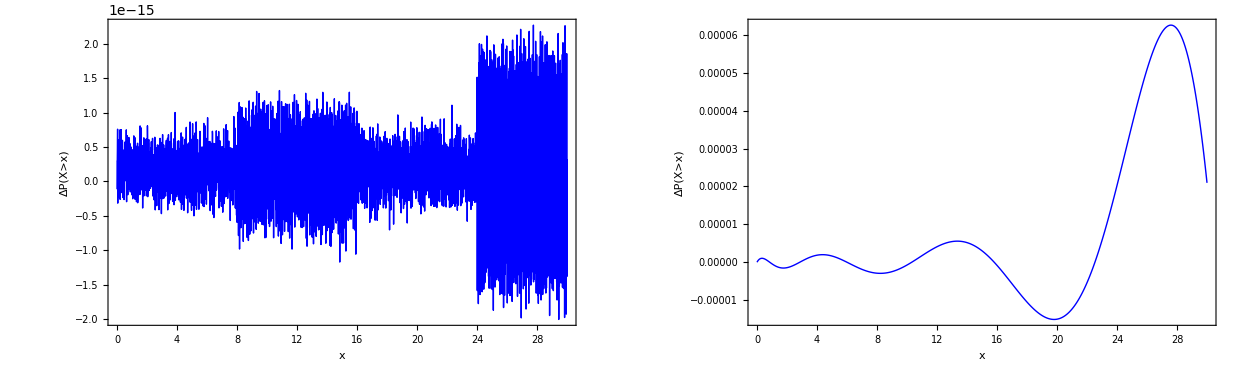

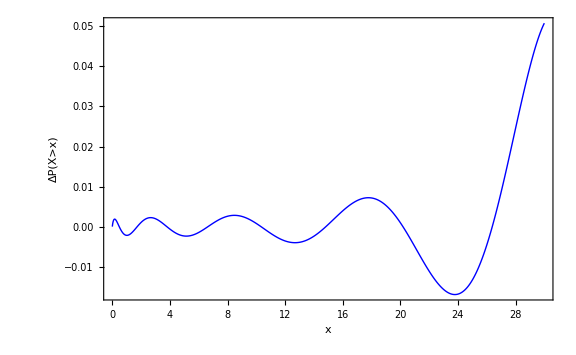

```mathematica
(*Fonction de survie de probabilité*)
GraphicsGrid[{{DiscretePlot[(SurvivalCompoundPoissonGammaPolynomial[[1]]-NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50])/NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50],{u,0,umax,1/100},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Parametrisation 1",24]}},ImageSize->Large,PlotStyle->Blue],
DiscretePlot[(SurvivalCompoundPoissonGammaPolynomial[[2]]-NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50])/NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50],{u,0,umax,1/100},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Parametrisation 2",24]}},ImageSize->Large,PlotStyle->Blue]}}]
GraphicsGrid[{{DiscretePlot[(SurvivalCompoundPoissonGammaPolynomial[[3]]-NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50])/NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50],{u,0,umax,1/100},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Parametrisation 3",24]}},ImageSize->Large,PlotStyle->Blue]
}}]
```

```mathematica
(*Tableau fonction de survie et erreur relative sur la fonction de survie Pour les différentes paramétrisation*)
TeXForm[Table[{N[k],N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]],N[SurvivalCompoundPoissonGammaPolynomial[[1]]/.u->k],N[SurvivalCompoundPoissonGammaPolynomial[[2]]/.u->k],N[SurvivalCompoundPoissonGammaPolynomial[[3]]/.u->k]},{k,umax/10,umax,umax/10}]]
```

\left(
\begin{array}{ccccc}
 3. & 0.806382 & 0.806382 & 0.806382 & 0.807966 \\
 6. & 0.573092 & 0.573092 & 0.573092 & 0.572258 \\
 9. & 0.364357 & 0.364357 & 0.364356 & 0.365284 \\
 12. & 0.21241 & 0.21241 & 0.212411 & 0.21165 \\
 15. & 0.115555 & 0.115555 & 0.115555 & 0.115619 \\
 18. & 0.0594094 & 0.0594094 & 0.0594088 & 0.0598344 \\
 21. & 0.0291366 & 0.0291366 & 0.0291363 & 0.028992 \\
 24. & 0.0137285 & 0.0137285 & 0.0137288 & 0.0134971 \\
 27. & 0.00624886 & 0.00624886 & 0.00624924 & 0.00630265 \\
 30. & 0.00275979 & 0.00275979 & 0.00275985 & 0.00289996 \\
\end{array}
\right)

```mathematica
TeXForm[Table[{N[k],N[Round[(N[SurvivalCompoundPoissonGammaPolynomial[[1]]/.u->k]-N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]])/N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]]*100*10^5]*10^-5],N[Round[(N[SurvivalCompoundPoissonGammaPolynomial[[2]]/.u->k]-N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]])/N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]]*100*10^5]*10^-5],N[Round[(N[SurvivalCompoundPoissonGammaPolynomial[[3]]/.u->k]-N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]])/N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]]*100*10^5]*10^-5]},{k,umax/10,umax,umax/10}]]
```

\left(
\begin{array}{cccc}
 3. & 0. & 0.00003 & 0.19645 \\
 6. & 0. & 0. & -0.14558 \\
 9. & 0. & -0.00025 & 0.25437 \\
 12. & 0. & 0.00041 & -0.3579 \\
 15. & 0. & 0.0003 & 0.05592 \\
 18. & 0. & -0.00105 & 0.71535 \\
 21. & 0. & -0.00124 & -0.49631 \\
 24. & 0. & 0.00203 & -1.6853 \\
 27. & 0. & 0.00607 & 0.8607 \\
 30. & 0. & 0.0021 & 5.07896 \\
\end{array}
\right)

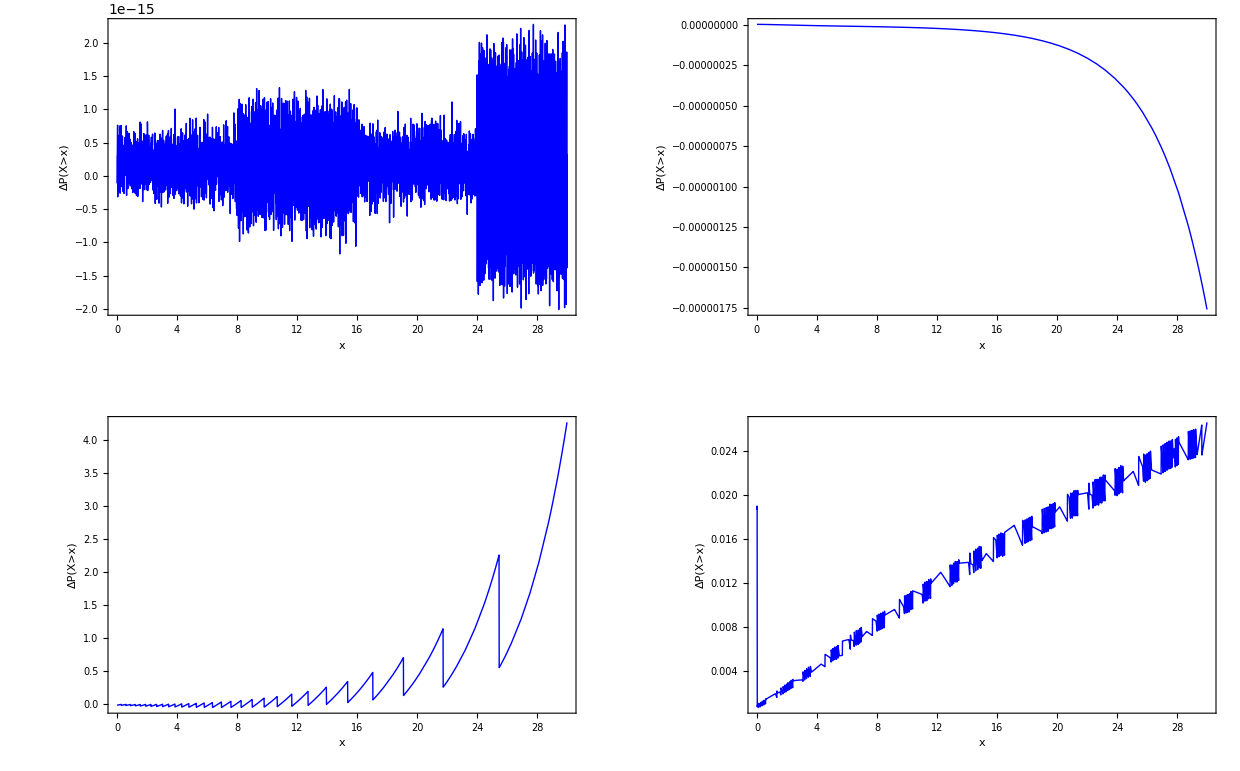

```mathematica
GraphicsGrid[{
{DiscretePlot[(SurvivalCompoundPoissonGammaPolynomial[[1]]-NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50])/NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50],{u,0,umax,1/100},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Polynomial",24]}},ImageSize->Large,PlotStyle->Blue],
Plot[(SurvivalCompoundPoissonGammaFFT[mFFT,bFFT,u,nFFT,λ,α,β]-NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50])/NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50],{u,1/50,umax},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Fourier",24]}},ImageSize->Large,PlotStyle->Blue]},
{Plot[(SurvivalCompoundPoissonGammaMnats[λ,α,β,αMnats,bMnats,u]-NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50])/NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50],{u,0,umax},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Exponential Moments",24]}},ImageSize->Large,PlotStyle->Blue],
Plot[(SurvivalPoissonCompoundGammaPanger[VectProbaCompoundPoisson,h,u]-NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50])/NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50],{u,0,umax},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Panjer",24]}},ImageSize->Large,PlotStyle->Blue]}}]
```

```mathematica
(*Tableau fonction de survie et erreur relative sur la fonction de survie Pour les différentes méthodes numériques*)
TeXForm[Table[{N[k],N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]],N[SurvivalCompoundPoissonGammaPolynomial[[1]]/.u->k],N[SurvivalCompoundPoissonGammaFFT[mFFT,bFFT,k,nFFT,λ,α,β]],N[SurvivalCompoundPoissonGammaMnats[λ,α,β,αMnats,bMnats,k]],N[SurvivalPoissonCompoundGammaPanger[VectProbaCompoundPoisson,h,k]]},{k,umax/10,umax,umax/10}]]
```

\left(
\begin{array}{cccccc}
 3. & 0.806382 & 0.806382 & 0.806382 & 0.805233 & 0.808772 \\
 6. & 0.573092 & 0.573092 & 0.573092 & 0.560555 & 0.576346 \\
 9. & 0.364357 & 0.364357 & 0.364357 & 0.390845 & 0.367403 \\
 12. & 0.21241 & 0.21241 & 0.21241 & 0.220259 & 0.214731 \\
 15. & 0.115555 & 0.115555 & 0.115555 & 0.14352 & 0.117098 \\
 18. & 0.0594094 & 0.0594094 & 0.0594094 & 0.0785728 & 0.0603396 \\
 21. & 0.0291366 & 0.0291366 & 0.0291366 & 0.0521104 & 0.0296565 \\
 24. & 0.0137285 & 0.0137285 & 0.0137285 & 0.0305607 & 0.014002 \\
 27. & 0.00624886 & 0.00624886 & 0.00624886 & 0.0145444 & 0.00638581 \\
 30. & 0.00275979 & 0.00275979 & 0.00275979 & 0.0145444 & 0.00282554 \\
\end{array}
\right)

```mathematica
TeXForm[Table[{N[k],N[Round[(N[SurvivalCompoundPoissonGammaPolynomial[[1]]/.u->k]-N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]])/N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]]*100*10^5]*10^-5],N[Round[(N[SurvivalCompoundPoissonGammaFFT[mFFT,bFFT,k,nFFT,λ,α,β]]-N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]])/N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]]*100*10^5]*10^-5],N[Round[(N[SurvivalCompoundPoissonGammaMnats[λ,α,β,αMnats,bMnats,k]]-N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]])/N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]]*100*10^5]*10^-5],N[Round[(N[SurvivalPoissonCompoundGammaPanger[VectProbaCompoundPoisson,h,k]]-N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]])/N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]]*100*10^5]*10^-5]},{k,umax/10,umax,umax/10}]]
```

\left(
\begin{array}{ccccc}
 3. & 0. & 0. & -0.14243 & 0.29637 \\
 6. & 0. & 0. & -2.18774 & 0.56776 \\
 9. & 0. & 0. & 7.26981 & 0.83609 \\
 12. & 0. & 0. & 3.69503 & 1.09255 \\
 15. & 0. & 0. & 24.2007 & 1.33558 \\
 18. & 0. & -0.00001 & 32.2566 & 1.56579 \\
 21. & 0. & -0.00002 & 78.8485 & 1.78436 \\
 24. & 0. & -0.00003 & 122.608 & 1.99258 \\
 27. & 0. & -0.00008 & 132.753 & 2.19157 \\
 30. & 0. & -0.00018 & 427.012 & 2.38237 \\
\end{array}
\right)

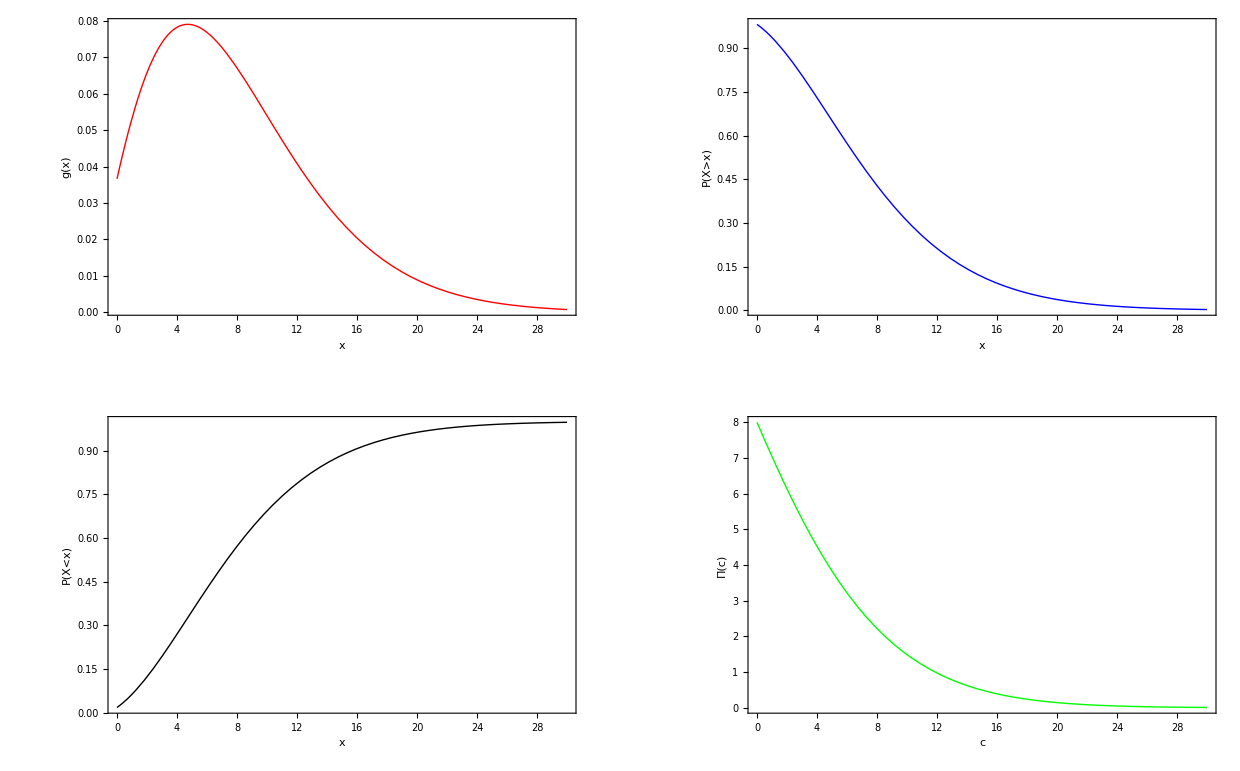

```mathematica
GraphicsGrid[{{Plot[DensityCompoundPoissonGammaPolynomial[[1]],{x,0,umax},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Filling->None,FrameLabel->{{Style["g(x)",24],None},{Style["x",24],Style["Probability Density Function",24]}},ImageSize->Large,PlotStyle->{Red,Thick}],
Plot[SurvivalCompoundPoissonGammaPolynomial[[1]],{u,0,umax},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Filling->None,FrameLabel->{{Style["P(X>x)",24],None},{Style["x",24],Style["Survival Function",24]}},ImageSize->Large,PlotStyle->{Blue,Thick}]},
{Plot[1-SurvivalCompoundPoissonGammaPolynomial[[1]],{u,0,umax},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Filling->None,FrameLabel->{{Style["P(X<x)",24],None},{Style["x",24],Style["Cumulative Distribution Function",24]}},ImageSize->Large,PlotStyle->{Black,Thick}],Plot[UsualStopLossCompoundPoissonGammaPolynomial,{c,0,umax},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Filling->None,FrameLabel->{{Style["Π(c)",24],None},{Style["c",24],Style["Usual Stop Loss Premium",24]}},ImageSize->Large,PlotStyle->{Green,Thick}]}}]
```

```mathematica
(*Stop Loss Premium par simulations*)
NObs=1000000;
SamplePoisson=RandomVariate[PoissonDistribution[λ],NObs];
SampleCompoundPoissonGamma=Table[Total[RandomVariate[GammaDistribution[α,β],SamplePoisson[[i]]]],{i,1,NObs,1}];
```

```mathematica
TeXForm[Table[{N[Retention],Mean[Table[Max[SampleCompoundPoissonGamma[[i]]-Retention,0],{i,1,NObs,1}]],N[UsualStopLossCompoundPoissonGammaPolynomial/.c->Retention],N[Round[((N[UsualStopLossCompoundPoissonGammaPolynomial/.c->Retention]-Mean[Table[Max[SampleCompoundPoissonGamma[[i]]-Retention,0],{i,1,NObs,1}]])/Mean[Table[Max[SampleCompoundPoissonGamma[[i]]-Retention,0]  ,{i,1,NObs,1}]])*100*10^5]*10^-5]},{Retention,umax/10,umax,umax/10}]]
```

\left(
\begin{array}{cccc}
 3. & 5.27937 & 5.28977 & 0.19704 \\
 6. & 3.21013 & 3.2187 & 0.26682 \\
 9. & 1.81787 & 1.82481 & 0.38157 \\
 12. & 0.969839 & 0.974639 & 0.49493 \\
 15. & 0.49123 & 0.494874 & 0.74191 \\
 18. & 0.237786 & 0.240618 & 1.1907 \\
 21. & 0.110721 & 0.112688 & 1.77607 \\
 24. & 0.0498302 & 0.0510734 & 2.49487 \\
 27. & 0.0217394 & 0.0224882 & 3.44426 \\
 30. & 0.00939161 & 0.00965032 & 2.75466 \\
\end{array}
\right)